# Competition between Weak Localization and Antilocalization in Topological Surface States

## Constants

```mathematica
Subscript[l, ϕ]=300 10^-9
Subscript[l, m]=1000 10^-9
(*{Slider[Dynamic[Subscript[n, m]],{0,10^25}],"n_m",Dynamic[Subscript[n, m]]}*)
Subscript[n, m]=8.68 10^24
(*{Slider[Dynamic[Subscript[n, 0]],{0,10^25}],"n_0",Dynamic[Subscript[n, 0]]}*)
Subscript[n, 0]=5.67 10^24
(*{Slider[Dynamic[Subscript[u, 0]],{0,10}],"u_0",Dynamic[Subscript[u, 0]]}*)
Subscript[u, 0]=10
(*{Slider[Dynamic[Subscript[u, x]],{0,10}],"u_x and u_z",Dynamic[Subscript[u, x]]}*)
Subscript[u, x]=.09
Subscript[u, z]:=Subscript[u, x]
Subscript[e, f]=5 charge
γ=1

hbar :=1.05 10^-34
charge :=1.6 10^-19

nf = Subscript[e, f]/(2 Pi γ^2)
```

## Independent Parameters

B → Tesla
Δ/(2 E_F)→ Dimensionless

## Plots

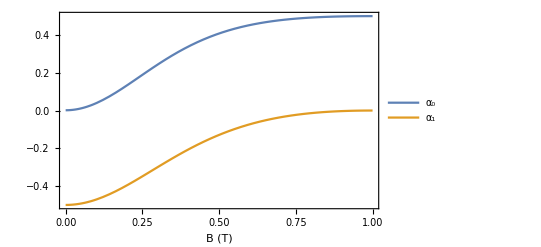
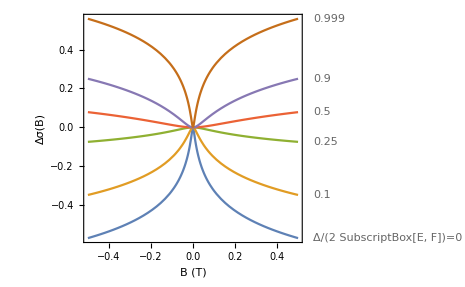
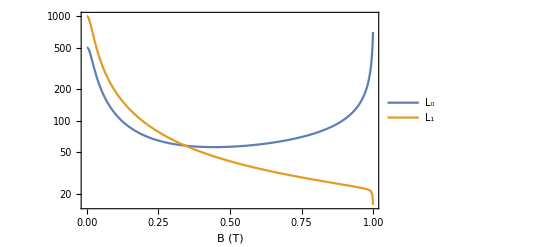

## Plots

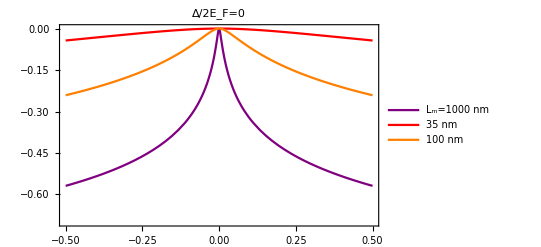
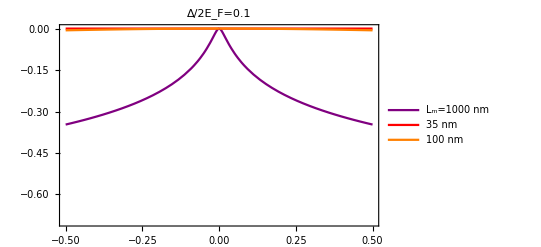
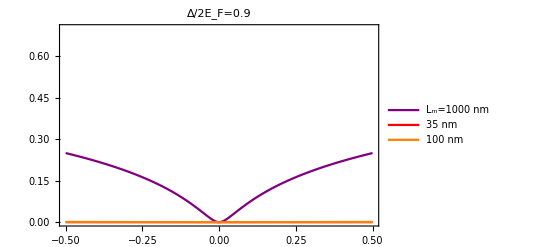
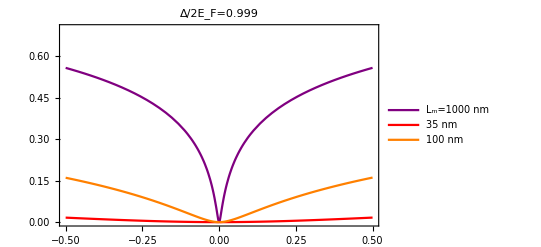

## Magnetoconductivity​

Δσ(B)=∑_(i=0)^1 (α_i e^2)/πh[Ψ(l_B^2/l_ϕ^2+l_B^2/l_i^2+1/2)-ln(l_B^2/l_ϕ^2+l_B^2/l_i^2)]

```mathematica
Δσ[B_,Db2Ef_]=∑_(i=0)^1 (Subscript[α, i][B,Db2Ef])/Pi (PolyGamma[lB2[B,Db2Ef]/(Subscript[l, ϕ]^2)+lB2[B, Db2Ef]/(Subscript[l2, i][B,Db2Ef])+1/2]-Log[lB2[B,Db2Ef]/Subscript[l, ϕ]^2+lB2[B,Db2Ef]/(Subscript[l2, i][B,Db2Ef]) ])
```

## h_z from hamiltonian

```mathematica
hzbyEf[B_,Db2Ef_]=(9.27 10^-24)/Subscript[e, f] B+ Db2Ef
```

## a and b

a = cos (θ/2)
b = sin (θ/2)

a2 = a^2
b2 = b^2

```mathematica
a2[B_,Db2Ef_]:=1/2+hzbyEf[B, Db2Ef]/2
```

```mathematica
b2[B_, Db2Ef_]:=1/2-hzbyEf[B, Db2Ef]/2
```

## Scattering Times

```mathematica
Subscript[τ, e][B_, Db2Ef_]:=hbar/(2 Pi nf Subscript[n, 0] Subscript[u, 0]^2(a2[B, Db2Ef]^2+b2[B,Db2Ef]^2))
```

```mathematica
Subscript[τ, x][B_, Db2Ef_]:=hbar/(2 Pi nf Subscript[n, m] Subscript[u, x]^2 2 a2[B, Db2Ef]b2[B, Db2Ef])
```

```mathematica
Subscript[τ, z][B_, Db2Ef_]:=hbar/(2 Pi nf Subscript[n, m] Subscript[u, z]^2  (a2[B, Db2Ef]^2+b2[B, Db2Ef]^2))
```

```mathematica
Subscript[τ, m][B_, Db2Ef_] :=1/(2/(Subscript[τ, x][B, Db2Ef])+1/(Subscript[τ, z][B, Db2Ef]))
```

```mathematica
Subscript[τ, 0][B_, Db2Ef_]:=1/(1/(Subscript[τ, e][B, Db2Ef])+1/(Subscript[τ, m][B, Db2Ef]))
```

## Cooperon Gaps

```mathematica
Subscript[g, 0][B_, Db2Ef_]:=2((a2[B,Db2Ef]^2+b2[B,Db2Ef]^2)/a2[B, Db2Ef]^2 (1/(Subscript[τ, 0][B, Db2Ef]))/(1/(Subscript[τ, e][B, Db2Ef])+1/(Subscript[τ, z][B, Db2Ef]))-1)
```

```mathematica
Subscript[g, 2][B_, Db2Ef_]:=2((a2[B,Db2Ef]^2+b2[B,Db2Ef]^2)/b2[B, Db2Ef]^2 (1/(Subscript[τ, 0][B, Db2Ef]))/(1/(Subscript[τ, e][B, Db2Ef])+1/(Subscript[τ, z][B, Db2Ef]))-1)
```

```mathematica
Subscript[g, 1][B_, Db2Ef_]:=2((1/(Subscript[τ, 0][B, Db2Ef]))/((1/(Subscript[τ, e][B, Db2Ef])-1/(Subscript[τ, z][B, Db2Ef])) (2 a2[B,Db2Ef]b2[B,Db2Ef])/(a2[B,Db2Ef]^2+b2[B,Db2Ef]^2)-2/(Subscript[τ, x][B, Db2Ef]))-1)
```

## Velocity Correction

```mathematica
Subscript[η, v][B_, Db2Ef_]:=(1-1/2((Subscript[τ, 0][B, Db2Ef])/(Subscript[τ, e][B, Db2Ef])-(Subscript[τ, 0][B, Db2Ef])/(Subscript[τ, z][B, Db2Ef])) (2 a2[B,Db2Ef] b2[B,Db2Ef])/(a2[B,Db2Ef]^2+b2[B,Db2Ef]^2))^-1
```

```mathematica
Subscript[η, H][B_, Db2Ef_]:=-1/2 (1-(Subscript[η, v][B, Db2Ef])^-1-(Subscript[τ, 0][B, Db2Ef])/(Subscript[τ, x][B, Db2Ef]))
```

## Alphas

```mathematica
Subscript[α, 1][B_, Db2Ef_]:=-(Subscript[η, v][B, Db2Ef])^2(1+2 Subscript[η, H][B, Db2Ef])/(2 (1+1/(Subscript[g, 0][B, Db2Ef])+1/(Subscript[g, 2][B, Db2Ef])))
```

```mathematica
Subscript[α, 0][B_, Db2Ef_]:=(Subscript[η, v][B, Db2Ef])^2(1+2 Subscript[η, H][B, Db2Ef])/(2 (1+1/(Subscript[g, 1][B, Db2Ef])))
```

```mathematica
DD[B_,Db2Ef_]:=Subscript[l, m]^2/(Subscript[τ, m][B, Db2Ef])
```

## Scattering Lengths

```mathematica
l2e[B_,Db2Ef_]:=DD[B,Db2Ef]Subscript[τ, e][B,Db2Ef](* = Subscript[l, e]^2 *)
```

```mathematica
l2[B_,Db2Ef_]:=(1/l2e[B,Db2Ef]+1/Subscript[l, m]^2)^-1(* = l^2 *)
```

```mathematica
Subscript[l2, 0][B_, Db2Ef_]:=(2 l2[B,Db2Ef]4 a2[B,Db2Ef] b2[B,Db2Ef](1+1/(Subscript[g, 1][B, Db2Ef])))/(Subscript[g, 0][B, Db2Ef])(* = Subscript[l, 0]^2 *)
```

```mathematica
Subscript[l2, 1][B_, Db2Ef_]:=(2 l2[B,Db2Ef] 4a2[B,Db2Ef]b2[B,Db2Ef](1+1/(Subscript[g, 0][B, Db2Ef])+1/(Subscript[g, 2][B, Db2Ef])))/(Subscript[g, 1][B, Db2Ef])(* = Subscript[l, 1]^2 *)
```

```mathematica
lB2[B_, Db2Ef_]:=hbar/(4 charge Abs[ B]) (* = Subscript[l, B]^2 *)
```